## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.3; qscal=0.6; Q=0.99;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.326565+2.22169×10^-9 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.520565

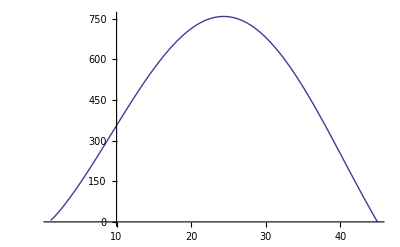

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<176,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,175}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,175}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,200}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,200}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{45.,2.22184×10^-9},{44.8,2.28172×10^-9},{44.6,2.34408×10^-9},{44.4,2.41267×10^-9},{44.2,2.47308×10^-9},{44.,2.54075×10^-9},{43.8,2.6104×10^-9},{43.6,2.68214×10^-9},{43.4,2.7562×10^-9},{43.2,2.83248×10^-9},{43.,2.91102×10^-9},{42.8,2.99125×10^-9},{42.6,3.07532×10^-9},{42.4,3.16202×10^-9},{42.2,3.25039×10^-9},{42.,3.34182×10^-9},{41.8,3.43622×10^-9},{41.6,3.53349×10^-9},{41.4,3.63378×10^-9},{41.2,3.73729×10^-9},{41.,3.84403×10^-9},{40.8,3.95414×10^-9},{40.6,4.06779×10^-9},{40.4,4.18501×10^-9},{40.2,4.30633×10^-9},{40.,4.48321×10^-9},{39.8,4.55966×10^-9},{39.6,4.69263×10^-9},{39.4,4.82989×10^-9},{39.2,4.97162×10^-9},{39.,5.11769×10^-9},{38.8,5.28039×10^-9},{38.6,5.42504×10^-9},{38.4,5.58616×10^-9},{38.2,5.75246×10^-9},{38.,5.9243×10^-9},{37.8,6.10205×10^-9},{37.6,6.28548×10^-9},{37.4,6.47507×10^-9},{37.2,6.67136×10^-9},{37.,6.87345×10^-9},{36.8,7.08254×10^-9},{36.6,7.29882×10^-9},{36.4,7.52231×10^-9},{36.2,7.75344×10^-9},{36.,7.99234×10^-9},{35.8,8.2394×10^-9},{35.6,8.49491×10^-9},{35.4,8.75914×10^-9},{35.2,9.03246×10^-9},{35.,9.31449×10^-9},{34.8,9.6077×10^-9},{34.6,9.91031×10^-9},{34.4,1.02233×10^-8},{34.2,1.05475×10^-8},{34.,1.08824×10^-8},{33.8,1.12197×10^-8},{33.6,1.15894×10^-8},{33.4,1.19614×10^-8},{33.2,1.23465×10^-8},{33.,1.27453×10^-8},{32.8,1.31583×10^-8},{32.6,1.35859×10^-8},{32.4,1.40289×10^-8},{32.2,1.44879×10^-8},{32.,1.49633×10^-8},{31.8,1.54559×10^-8},{31.6,1.59662×10^-8},{31.4,1.64956×10^-8},{31.2,1.70434×10^-8},{31.,1.76098×10^-8},{30.8,1.82002×10^-8},{30.6,1.88107×10^-8},{30.4,1.94437×10^-8},{30.2,2.00998×10^-8},{30.,2.07804×10^-8},{29.8,2.14861×10^-8},{29.6,2.22181×10^-8},{29.4,2.29773×10^-8},{29.2,2.37649×10^-8},{29.,2.45818×10^-8},{28.8,2.54301×10^-8},{28.6,2.63093×10^-8},{28.4,2.72227×10^-8},{28.2,2.8169×10^-8},{28.,2.91524×10^-8},{27.8,3.01726×10^-8},{27.6,3.12322×10^-8},{27.4,3.23348×10^-8},{27.2,3.34738×10^-8},{27.,3.4654×10^-8},{26.8,3.58904×10^-8},{26.6,3.71715×10^-8},{26.4,3.84966×10^-8},{26.2,3.9875×10^-8},{26.,4.13072×10^-8},{25.8,4.27945×10^-8},{25.6,4.43397×10^-8},{25.4,4.59451×10^-8},{25.2,4.76129×10^-8},{25.,4.93452×10^-8},{24.8,5.11452×10^-8},{24.6,5.30158×10^-8},{24.4,5.49591×10^-8},{24.2,5.69784×10^-8},{24.,5.90771×10^-8},{23.8,6.12576×10^-8},{23.6,6.35262×10^-8},{23.4,6.58779×10^-8},{23.2,6.83248×10^-8},{23.,7.08673×10^-8},{22.8,7.351×10^-8},{22.6,7.62555×10^-8},{22.4,7.91086×10^-8},{22.2,8.2073×10^-8},{22.,8.5153×10^-8},{21.8,8.83537×10^-8},{21.6,9.16779×10^-8},{21.4,9.51319×10^-8},{21.2,9.87195×10^-8},{21.,1.02446×10^-7},{20.8,1.06316×10^-7},{20.6,1.10334×10^-7},{20.4,1.14506×10^-7},{20.2,1.18833×10^-7},{20.,1.23334×10^-7},{19.8,1.27995×10^-7},{19.6,1.32831×10^-7},{19.4,1.37854×10^-7},{19.2,1.43058×10^-7},{19.,1.48449×10^-7},{18.8,1.54044×10^-7},{18.6,1.59831×10^-7},{18.4,1.65826×10^-7},{18.2,1.72037×10^-7},{18.,1.7846×10^-7},{17.8,1.85103×10^-7},{17.6,1.91965×10^-7},{17.4,1.99058×10^-7},{17.2,2.06378×10^-7},{17.,2.13932×10^-7},{16.8,2.21707×10^-7},{16.6,2.29708×10^-7},{16.4,2.37959×10^-7},{16.2,2.46421×10^-7},{16.,2.55113×10^-7},{15.8,2.64025×10^-7},{15.6,2.73132×10^-7},{15.4,2.82428×10^-7},{15.2,2.91857×10^-7},{15.,3.01548×10^-7},{14.8,3.1132×10^-7},{14.6,3.21198×10^-7},{14.4,3.3114×10^-7},{14.2,3.41098×10^-7},{14.,3.51022×10^-7},{13.8,3.60855×10^-7},{13.6,3.7047×10^-7},{13.4,3.79803×10^-7},{13.2,3.8867×10^-7},{13.,3.96951×10^-7},{12.8,4.04406×10^-7},{12.6,4.10779×10^-7},{12.4,4.1571×10^-7},{12.2,4.18755×10^-7},{12.,4.19327×10^-7},{11.8,4.16654×10^-7},{11.6,4.09718×10^-7},{11.4,3.97152×10^-7},{11.2,3.77079×10^-7},{11.,3.46991×10^-7},{10.8,3.03392×10^-7},{10.6,2.41464×10^-7},{10.4,1.54454×10^-7},{10.2,3.28331×10^-8},{10.,-1.36896×10^-7},{9.8,-3.74099×10^-7},{9.6,-7.06496×10^-7},{9.4,-1.17465×10^-6},{9.2,-1.83755×10^-6},{9.,-2.7821×10^-6},{8.8,-4.13669×10^-6},{8.6,-6.09267×10^-6},{8.4,-8.93599×10^-6},{8.2,-0.0000130965},{8.,-0.0000192225},{7.8,-0.000028295},{7.6,-0.0000417998},{7.4,-0.000061988},{7.2,-0.0000922618},{7.,-0.000137739},{6.8,-0.000206054},{6.6,-0.000308462},{6.4,-0.000461284},{6.2,-0.000687668},{6.,-0.00101956},{5.8,-0.00149962},{5.6,-0.00218277},{5.4,-0.00313691},{5.2,-0.00444277},{5.,-0.00619291}}

```mathematica
(*The imaginary part vs the radius*)
```

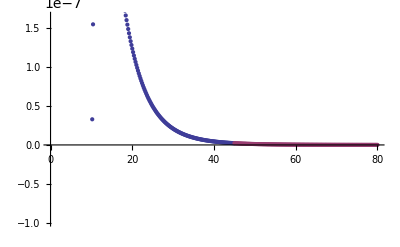

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

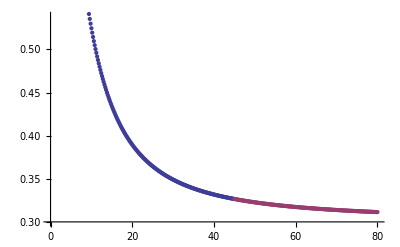

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio2.0/Q=0.990/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio2.0/Q=0.990/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio2.0/Q=0.990/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio2.0/Q=0.990/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```